# Physics through Computational Thinking Week-2: Dimensional Analysis and Scales of Physical Problems

In this week, we introduce dimensional analysis and non-dimensionalization as essential tools for understanding physical systems. By identifying the natural scales of a problem, we simplify equations, reduce the number of parameters

## 1. Non-Dimensionalization

The aim is to reduce the number of parameters. In a Spring-Mass system, instead of tracking m, k, and t, we use a single dimensionless time τ.

The Parametric View

Example equation:   m d^2/dt^2 x + k x=0       -- (1)

Natural time scale:   t_0 = √(m/k)
Define dimensionless time (τ) :   t = t_0τ
 
 Eq. (1) becomes,  d^2/dτ^2 x(τ)+x(τ)=0

This is a dimensionless equation. One equation fits all masses and springs - only one parameter. 

A solution is:   x(τ)=cos(τ)  ,  v(τ)=d/dτ x(τ)=-sin(τ)

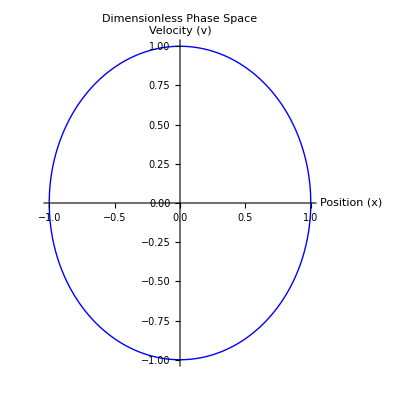

```mathematica
ParametricPlot[{Cos[tau],-Sin[tau]},{tau,0,2 Pi},PlotStyle->{Thick,Blue},AspectRatio->1,AxesLabel->{"Position (x)","Velocity (v)"},PlotLabel->"Dimensionless Phase Space"]
```

This space is called phase space. The radius corresponds to the total (dimensionless) energy. This is the geometric representation of an ideal harmonic oscillator.

```mathematica
SHM=NDSolveValue[{x''[tau]+x[tau]==0,x[0]==1,x'[0]==0},x,{tau,0,20}];
```

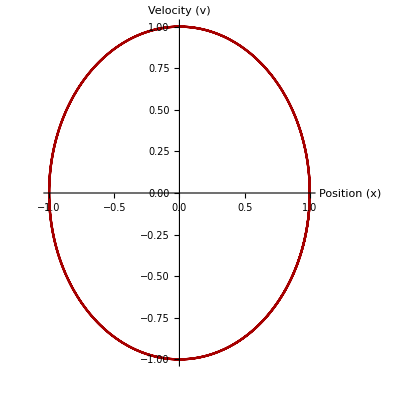

```mathematica
ParametricPlot[{SHM[tau],SHM'[tau]},{tau,0,20},AxesLabel->{"Position (x)","Velocity (v)"}]
```

```mathematica
Table[NDSolveValue[{x''[t]+x[t]==0,x[0]==a,x'[0]==0},x,{t,0,10}],{a,{0.5,1,2}}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

Each element is an InterpolatingFunction representing motion with a different initial displacement. Follow-up visualization:

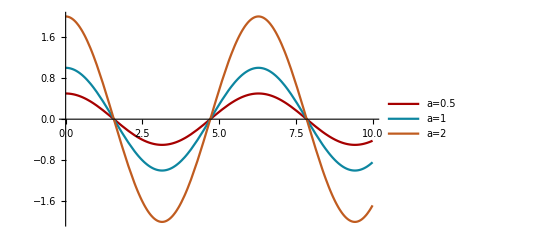

```mathematica
Plot[Evaluate@Table[sol[t],{sol,%} ],{t,0,10},PlotLegends->{"a=0.5","a=1","a=2"}]
```

Ex-1: Add damping and observe how the phase‑space trajectory changes.

Damped oscillator

m d^2/dt^2 x+c d/dt x+k x =0

Natural time scale:   t_0 = √(m/k)
Dimensionless form :   d^2/dτ^2 x+γ d/dτ x+x =0 , where γ= c/(√(m k))

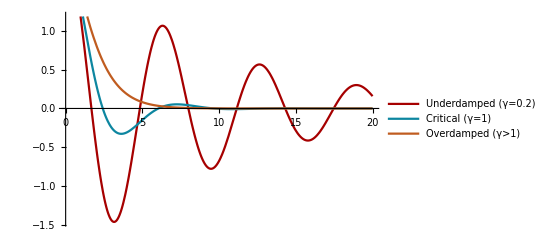

```mathematica
sol[γ_]:=NDSolveValue[{x''[t]+γ x'[t]+x[t]==0,x[0]==2,x'[0]==0},x,{t,0,20}]

Plot[Evaluate@Table[sol[γ][t],{γ,{0.2,1,2}}],{t,0,20},PlotLegends->{"Underdamped (γ=0.2)","Critical (γ=1)","Overdamped (γ>1)"}]
```

```mathematica
Manipulate[dampedSol=NDSolveValue[{x''[t]+gamma x'[t]+x[t]==0,x[0]==1,x'[0]==0},x,{t,0,50}];
Plot[dampedSol[t],{t,0,50},PlotRange->{-1,1}],{{gamma,0.1,"Damping Coefficient (γ) "},0,4}]
```

Ex-2: Change initial conditions and observe the effect.

Driven oscillator

d^2/dτ^2 x+ω_0 x=cos(ω τ)

Natural frequency of the oscillator:   ω_0=1

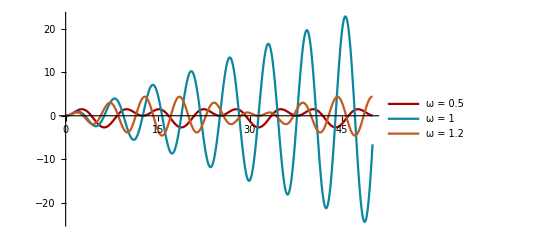

```mathematica
solD[ω_]:=NDSolveValue[{x''[t]+x[t]==Cos[ω t],x[0]==0,x'[0]==0},x,{t,0,50}]

Plot[Evaluate@Table[solD[ω][t],{ω,{0.5,1,1.2}}],{t,0,50},PlotLegends->{"ω = 0.5","ω = 1","ω = 1.2"},PlotRange->All]
```

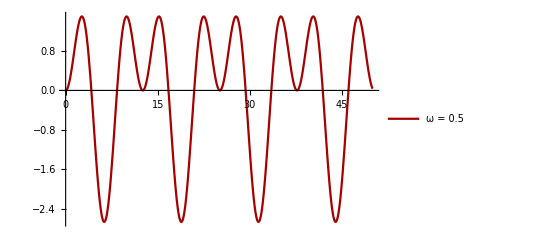

```mathematica
solD[ω_]:=NDSolveValue[{x''[t]+x[t]==Cos[ω t],x[0]==0,x'[0]==0},x,{t,0,50}]

Plot[Evaluate@Table[solD[ω][t],{ω,{0.5}}],{t,0,50},PlotLegends->{"ω = 0.5"},PlotRange->All]
```

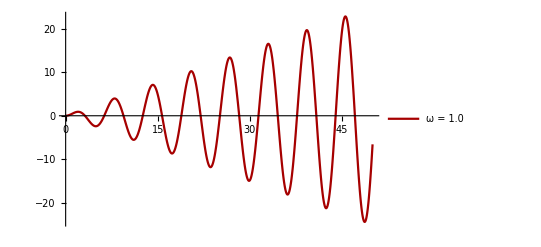

```mathematica
solD[ω_]:=NDSolveValue[{x''[t]+x[t]==Cos[ω t],x[0]==0,x'[0]==0},x,{t,0,50}]

Plot[Evaluate@Table[solD[ω][t],{ω,{1.0}}],{t,0,50},PlotLegends->{"ω = 1.0"},PlotRange->All]
```

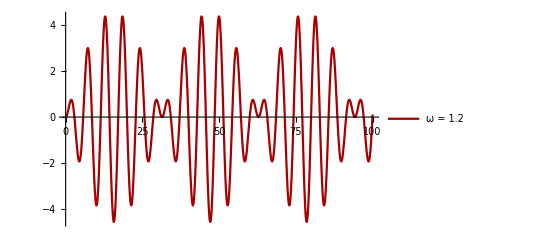

```mathematica
solD[ω_]:=NDSolveValue[{x''[t]+x[t]==Cos[ω t],x[0]==0,x'[0]==0},x,{t,0,100}]

Plot[Evaluate@Table[solD[ω][t],{ω,{1.2}}],{t,0,100},PlotLegends->{"ω = 1.2"},PlotRange->All]
```

This plot shows:
 (i)  ω = 0.5 → slow driving (oscillations with small amplitude)
 (ii) ω = 1.0 → resonance (ω=ω_0)
(iii) ω = 1.2 → off-resonance (bounded oscillation)

Anharmonic Oscillator

In the real world, springs aren't perfectly linear. The Duffing Oscillator adds a cubic term x^3. This introduces "Anharmonicity", where the period depends on the amplitude. The equation is

d^2/dτ^2 x+x+4λ x^3=0

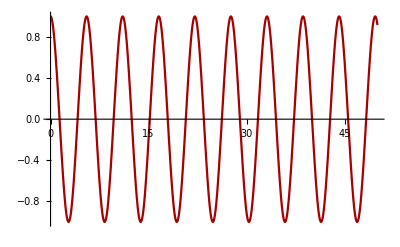

```mathematica
λ=0.1;
anh=NDSolveValue[{x''[t]+x[t]+4 λ x[t]^3==0,x[0]==1,x'[0]==0},x,{t,0,50}];
Plot[anh[t],{t,0,50}]
```

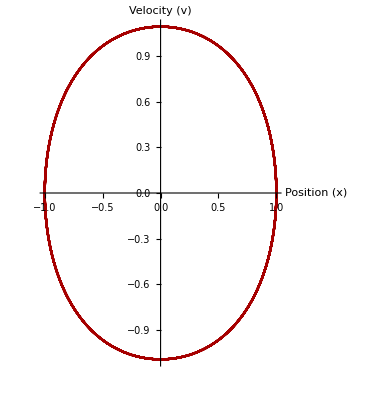

```mathematica
ParametricPlot[{anh[t],anh'[t]},{t,0,50},AxesLabel->{"Position (x)","Velocity (v)"}]
```

Note: motion is no longer sinusoidal.

## 2. Mathematical properties of Sequences

The Fibonacci Sequence

The Fibonacci sequence is defined by the recurrence relation:

F_n = F_(n-1) + F_(n-2)

with seed values F_0 = 0 and F_1 = 1.

```mathematica
fibo[0]=0;
fibo[1]=1;
fibo[n_]:=fibo[n]=fibo[n-1]+fibo[n-2];
```

```mathematica
Table[fibo[i],{i,0,15}] (*Generate the first 15 terms*)
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610}

```mathematica
377+610
```

987

```mathematica
fibo[16]
```

987

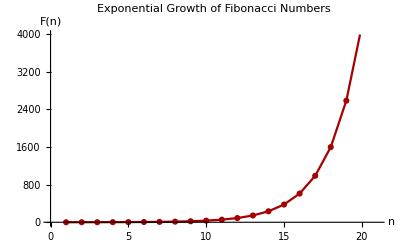

```mathematica
ListLinePlot[Table[fibo[i],{i,0,20}],PlotMarkers->Automatic,PlotLabel->"Exponential Growth of Fibonacci Numbers",AxesLabel->{"n","F(n)"}]
```

As n increases, the ratio of successive Fibonacci numbers (F_(n+1))/F_n converges to the Golden Ratio:

ϕ = (1+√5)/2

```mathematica
ratios=Table[N[fibo[i+1]/fibo[i],40],{i,1,40}]
```

{1.,2.,1.5,1.666666666666666666666666666666666666667,1.6,1.625,1.615384615384615384615384615384615384615,1.619047619047619047619047619047619047619,1.617647058823529411764705882352941176471,1.618181818181818181818181818181818181818,1.617977528089887640449438202247191011236,1.618055555555555555555555555555555555556,1.618025751072961373390557939914163090129,1.618037135278514588859416445623342175066,1.618032786885245901639344262295081967213,1.618034447821681864235055724417426545086,1.618033813400125234815278647463994990607,1.61803405572755417956656346749226006192,1.618033963166706529538387945467591485291,1.618033998521803399852180339985218033999,1.618033985017357938973140873378403069614,1.618033990175597086556377392580881937779,1.61803398820532505147084481976480441079,1.618033988957902001380262249827467218772,1.618033988670443185604798400533155614795,1.618033988780242682856507376866870412627,1.618033988738303006852732437963934058997,1.618033988754322537608830405492572629645,1.618033988748203621343798191078293911856,1.618033988750540839382721984519975001202,1.618033988749648101530971893432887483854,1.618033988749989097047296779290725053241,1.618033988749858848350071980248415554997,1.618033988749908598925421457588060222831,1.618033988749889595896597819661196222364,1.618033988749896854407719255379913346986,1.618033988749894081903178586045254006188,1.618033988749895140905679158315141341105,1.618033988749894736402718110837895704559,1.618033988749894890909100680999418033989}

```mathematica
ListLinePlot[ratios,GridLines->{None,{GoldenRatio}},PlotStyle->Red,PlotLabel->"Convergence to Golden Ratio",PlotRange->All]
```

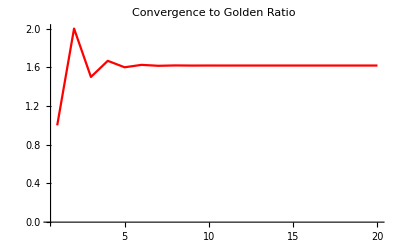

```mathematica
N[(1+√5)/2,40]
```

1.61803398874989484820458683436563811772

Lucas Sequence

The Lucas sequence L_n uses the same recurrence relation as Fibonacci, but with different initial conditions:   L_0=2  and L_1=1.

```mathematica
lucas[0]=2;
lucas[1]=1;
lucas[n_]:=lucas[n]=lucas[n-1]+lucas[n-2];
```

```mathematica
Table[{fibo[i],lucas[i]},{i,0,10}]//TableForm (*Compare Fibonacci and Lucas*)
```

0 | 2
1 | 1
1 | 3
2 | 4
3 | 7
5 | 11
8 | 18
13 | 29
21 | 47
34 | 76
55 | 123

```mathematica
ratios=Table[N[lucas[i+1]/lucas[i],40],{i,1,30}]
```

{3.,1.333333333333333333333333333333333333333,1.75,1.571428571428571428571428571428571428571,1.636363636363636363636363636363636363636,1.611111111111111111111111111111111111111,1.620689655172413793103448275862068965517,1.617021276595744680851063829787234042553,1.618421052631578947368421052631578947368,1.617886178861788617886178861788617886179,1.618090452261306532663316582914572864322,1.618012422360248447204968944099378881988,1.618042226487523992322456813819577735125,1.618030842230130486358244365361803084223,1.618035190615835777126099706744868035191,1.618033529678296329859537834164023561396,1.618034164099691963035564267712125455055,1.618033921772239529248875043267566632053,1.618034014333083752272970371162691196919,1.618033978977986381966021022013618033979,1.618033992482431769897042000326850792613,1.618033987324192611670833017700679241472,1.618033989294464645203576834844488834095,1.6180339885418876950676105784996431396,1.618033988829346510810021399490942471731,1.618033988719547013553490051318324657479,1.618033988761486689556561415651952168013,1.618033988745467158800360797977054712114,1.618033988751586075065378035936830076245,1.618033988749248857026452057459884396543}

Higher-Order: The Tribonacci Sequence

What if you sum the last three terms instead of two?

T_n = T_(n-1) + T_(n-2) + T_(n-3)

```mathematica
tribo[0]=0;
tribo[1]=0;
tribo[2]=1;
tribo[n_]:=tribo[n]=tribo[n-1]+tribo[n-2]+tribo[n-3];
```

```mathematica
Table[tribo[i],{i,0,15}]
```

{0,0,1,1,2,4,7,13,24,44,81,149,274,504,927,1705}

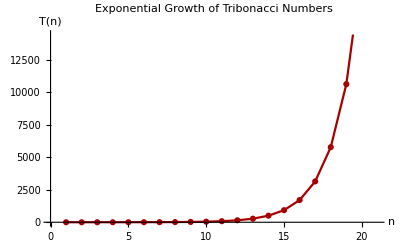

```mathematica
ListLinePlot[Table[tribo[i],{i,0,20}],PlotMarkers->Automatic,PlotLabel->"Exponential Growth of Tribonacci Numbers",AxesLabel->{"n","T(n)"}]
```

Generalizing: The Linear Recurrence Tool

Mathematica has a powerful built-in for any sequence of this type: LinearRecurrence.
Define rule: [{coeff1,coeff2,...},{seeds}, #number-of-terms]

```mathematica
LinearRecurrence[{2,1},{0,1},10](*Example:A sequence where Subscript[x, n]=2 Subscript[x, n-1]+1 Subscript[x, n-2] *)
```

{0,1,2,5,12,29,70,169,408,985}

```mathematica
LinearRecurrence[{1,1},{0,1},15]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377}

{0, 1, 1, 2, 3, 5, 8, 13, 21, 34, 55, 89, 144, 233, 377, 610}

```mathematica
LinearRecurrence[{1,1,1},{0,0,1},15]
```

{0,0,1,1,2,4,7,13,24,44,81,149,274,504,927}

{0, 0, 1, 1, 2, 4, 7, 13, 24, 44, 81, 149, 274, 504, 927, 1705}

Problem-1:

For the Sequence,   x_(n+1)=7/2 log(x_n)+2/7 x_n ,  with   x_0>1.4 
 (ii)  Find the convergence value.

```mathematica
f[x_]:=(2/7)*x+(7/2)*Log[x];

x0=1.5; (* initial point > 1.4 *)
iterations=1000;
sequence=NestList[f,x0,iterations];
```

```mathematica
Print["First 5 terms: ",Take[sequence,5]]
Print["Converged value (numerical): ",Last[sequence]]
```

First 5 terms: {1.5,1.8477,2.67671,4.21083,6.2349}

Converged value (numerical): 12.2951

```mathematica
fixedPoint=FindRoot[L==f[L],{L,1}]
```

{L→1.30522}

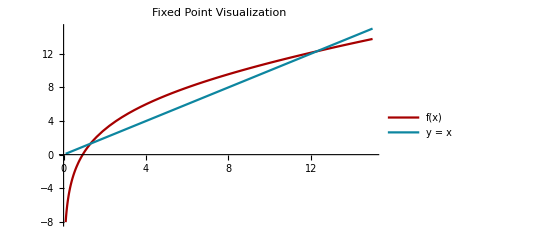

```mathematica
Plot[{f[x],x},{x,0.1,15},PlotLegends->{"f(x)","y = x"},PlotLabel->"Fixed Point Visualization"]
```

```mathematica
f[L]/.{L->1.305219679097998}
```

1.30522

Problem-2:

For the Series ,  s=∑ 1/n^(log n)where  n->[1,∞].

(ii)  Find the convergence value .

```mathematica
s=NSum[n^-Log[n],{n,1,Infinity},WorkingPrecision->20]
```

2.238181307

```mathematica
N[s,6]
```

2.23818

For the Series ,  s=∑ 1/(n^4 √(log n))where  n->[2,∞].

```mathematica
s=NSum[1/(n^4 √Log[n]),{n,2,Infinity},WorkingPrecision->20]
```

0.09281634736

```mathematica
N[s,7]
```

0.09281635

Problem-3:

For Fibonacci numbers F_n, the quantity 
r=(F_(n+2))/F_n-F_n/(F_(n+2)) converges to ... (up to three significant digit)

```mathematica
r[n_]:=Fibonacci[n+2]/Fibonacci[n]-Fibonacci[n]/Fibonacci[n+2];
```

```mathematica
Limit[r[n],n->Infinity]
```

√5

```mathematica
N[Limit[r[n],n->Infinity],3]
```

2.24

## 3. Plotting a Falling Object

You are standing on the roof of a building (1 meters high) and toss a ball upward at a speed of  9 m/s. We want to use Mathematica to track where the ball is at any given time.

Let’s consider the height (y) at any time (t) like this:

                                                           y(t)=-1/2 gt^2+v_0 t+y_0

```mathematica
g=9.8;
v0=9.0;
y0=1.0;
```

```mathematica
y[t_]:=-1/2*g*t^2+v0*t+y0;
```

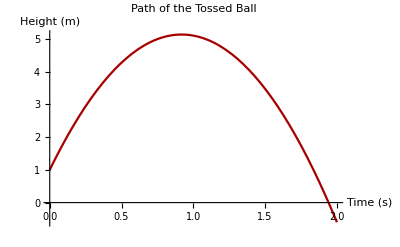

```mathematica
Plot[y[t],{t,0,2},AxesLabel->{"Time (s)","Height (m)"},PlotLabel->"Path of the Tossed Ball"]
```